## Potential Derivatives Series Expansions

With these rules in place we can write code to do this differentiation automatically, but for performance reasons and to show the procedure out we’ll do up to the fourth derivatives by hand

### Derivatives to Target

Basically we’ll want

∇_Q V = (∂/(∂Q_1) | ⋯ | ∂/(∂Q_m))V
∇_(Q^2) V = (∂^2/(∂Q_1 Q_1)V | ⋯ | ∂^2/(∂Q_1 Q_m)V
⋮ | ⋱ | ⋮
∂^2/(∂Q_1 Q_m)V | ⋯ | ∂^2/(∂Q_m Q_m)V)

and higher up to order 4.

We don’t actually have these directly, though, so we’ll need to build them using the chain rule a bunch from the components we do have.

As a simple initial example, we want

∇_Q V = (∂/(∂Q_1) | ⋯ | ∂/(∂Q_m))V

and we can look at this element wise as

(∇_Q V)_i=∂/(∂Q_i)V=∑_j (∂x_j)/(∂Q_i)∂/(∂x_j)V

### General Layout

We have basically two types of terms here:

∇_Q x = ((∂x_1)/(∂Q_1) | ⋯ | (∂x_n)/(∂Q_1)
⋮ | ⋱ | ⋮
(∂x_1)/(∂Q_m) | ⋯ | (∂x_n)/(∂Q_m))

which is the Jacobian going from Cartesian coordinates to internal coordinate normal modes. We will also have higher order Jacobian type things.

∇_x V = (∂/(∂x_1) | ⋯ | ∂/(∂x_n))V

which is the gradient of V with respect to the Cartesian coordinates. We’ll also have higher order derivatives here.

I will denote higher derivatives by adding an exponent to the dependent variable, e.g.

∇_(Q^2) x =(∂/(∂Q_1)((∂x_1)/(∂Q_1) | ⋯ | (∂x_n)/(∂Q_1)
⋮ | ⋱ | ⋮
(∂x_1)/(∂Q_m) | ⋯ | (∂x_n)/(∂Q_m)) | ⋯ | ∂/(∂Q_m)((∂x_1)/(∂Q_1) | ⋯ | (∂x_n)/(∂Q_1)
⋮ | ⋱ | ⋮
(∂x_1)/(∂Q_m) | ⋯ | (∂x_n)/(∂Q_m)))=(((∂^2 x_1)/(∂Q_1 Q_1) | ⋯ | (∂^2 x_n)/(∂Q_1 Q_1)
⋮ | ⋱ | ⋮
(∂^2 x_1)/(∂Q_1 Q_m) | ⋯ | (∂^2 x_n)/(∂Q_1 Q_m)) | ⋯ | ((∂^2 x_1)/(∂Q_m Q_1) | ⋯ | (∂^2 x_n)/(∂Q_m Q_1)
⋮ | ⋱ | ⋮
(∂^2 x_1)/(∂Q_m Q_m) | ⋯ | (∂^2 x_n)/(∂Q_m Q_m)))

is the 3D tensor of second derivatives of Cartesian coordinates with respect to pairs of internal coordinate normal modes.

### First Derivatives

We want

∇_Q V = (∂/(∂Q_1) | ⋯ | ∂/(∂Q_m))V

By applying the chain rule and noting that V is a function of the Cartesian coordinates (x)

∇_Q V=∇_Q x⊙∇_x V
=x_Q V_x

### Second Derivatives

Here we take

∇_(Q^2) V=∇_Q (∇_Q V)
=(x_Q V_x)_Q

Recalling the product rule we have here and letting

A=x_Q
B=V_x

(AB)_Q=A_Q B+((A(B_Q))^(2:1))^(2:1)
=x_(Q^2)V_x+((x_Q((V_x)_Q))^(2:1))^(2:1)
=x_(Q^2)V_x+((x_Q(x_Q V_(x^2)))^(2:1))^(2:1)

we can then see that this second term can be reduced, keeping in mind that for A, B two-dimensional tensors,

(AB)^(2:1)=(B^(2:1)A^(2:1))

as this is just a transposition, so we get

((x_Q(x_Q V_(x^2)))^(2:1))^(2:1)=(((x_Q V_(x^2))^(2:1))^(2:1)x_Q^(2:1))
=x_Q V_(x^2)x_Q^(2:1)

and so

V_(Q^2)=x_(Q^2)V_x+x_Q V_(x^2)x_Q^(2:1)

##### Validation (Redo)

We’ll check this termwise

(x_(Q^2)V_x)_ij=(x_(Q^2))_(ij:)·V_x
=(((∂^2 x_n)/(∂Q_i∂Q_j))_(n=1,…,N))·(((∂V)/(∂x_n))_(n=1,…,N))
=∑_(n=1)^N (∂V)/(∂x_n)(∂^2 x_n)/(∂Q_i∂Q_j)
(((x_Q(x_Q V_(x^2)))^(2:1))^(2:1))_ij=((x_Q(x_Q V_(x^2)))^(2:1))_ji
=(x_Q)_(j:)·((x_Q V_(x^2))^(2:1))_(:i)
=(x_Q)_(j:)·(x_Q V_(x^2))_(i:)
=(x_Q)_(j:)·((x_Q_(i:))·V_(x^2))
=((∂x_m)/(∂Q_j))_m·(((∂x_n)/(∂Q_i))_n·((∂^2 V)/(∂x_n∂x_m))_n)_m
=∑_(n=1)^N ∑_(m=1)^N (∂x_m)/(∂Q_j)(∂x_n)/(∂Q_i)(∂^2 V)/(∂x_n∂x_m)

Put together

∇_(Q^2) V=∑_(n=1)^N (∂V)/(∂x_n)(∂^2 x_n)/(∂Q_i∂Q_j)+∑_(n=1)^N ∑_(m=1)^N (∂x_m)/(∂Q_j)(∂x_n)/(∂Q_i)(∂^2 V)/(∂x_n∂x_m)

### Third Derivatives

V_(Q^3)=(x_(Q^2)V_x+((x_Q(x_Q V_(x^2)))^(2:1))^(2:1))_Q
=(x_(Q^2)V_x)_Q+(((x_Q(x_Q V_(x^2)))^(2:1))^(2:1))_Q
=(x_(Q^2)V_x)_Q+(((x_Q(x_Q V_(x^2)))^(2:1))_Q)^(3:2)

At this point we’ll split into two terms. The first is pretty straightforward

(x_(Q^2)V_x)_Q=x_(Q^3)V_x+((x_(Q^2)((V_x)_Q))^(2:1))^(3:1)
=x_(Q^3)V_x+((x_(Q^2)(x_Q V_(x^2)))^(2:1))^(3:1)

The second is more complicated so we’ll use the procedure as before

A=x_Q
B=(x_Q V_(x^2))^(2:1)
(AB)_Q=A_Q B+((A(B_Q))^(2:1))^(a:1)
=(x_(Q^2)(x_Q V_(x^2)))^(2:1)+((x_Q(((x_Q V_(x^2))^(2:1))_Q))^(2:1))^(2:1)
(((x_Q V_(x^2))^(2:1))_Q)^(2:1)=(((x_Q V_(x^2))_Q)^(3:2))^(2:1)
=((x_Q V_(x^2))_Q)^(3:1)
=(x_(Q^2)V_(x^2)+((x_Q((V_(x^2))_Q))^(2:1))^(2:1))^(3:1)
=(x_(Q^2)V_(x^2))^(3:1)+(((x_Q((V_(x^2))_Q))^(2:1))^(2:1))^(3:1)
=(x_(Q^2)V_(x^2))^(3:1)+((x_Q((V_(x^2))_Q))^(2:1))^(2:1,3:1)
=(x_(Q^2)V_(x^2))^(3:1)+((x_Q(x_Q V_(x^3)))^(2:1))^(2:1,3:1)
((x_Q(((x_Q V_(x^2))^(2:1))_Q))^(2:1))^(2:1)=(x_Q((x_(Q^2)V_(x^2))^(3:1)+((x_Q(x_Q V_(x^3)))^(2:1))^(2:1,3:1)))^(2:1)
=((x_Q(x_(Q^2)V_(x^2)))^(3:1))^(2:1)+(x_Q(((x_Q(x_Q V_(x^3)))^(2:1))^(2:1,3:1)))^(2:1)

Then sticking these parts together we get

V_(Q^3)=x_(Q^3)V_x+((x_(Q^2)(x_Q V_(x^2)))^(2:1))^(3:1)+(x_(Q^2)(x_Q V_(x^2)))^(2:1)+((x_Q(x_(Q^2)V_(x^2)))^(3:1))^(2:1)+(x_Q(((x_Q(x_Q V_(x^3)))^(2:1))^(2:1,3:1)))^(2:1)

Intuitive Description

Ignoring the index jockeying, this is

V_(Q^3)=x_(Q^3)V_x+x_(Q^2)x_Q V_(x^2) +x_(Q^2)x_Q V_(x^2)+ x_Q x_(Q^2)V_(x^2)+x_Q x_Q x_Q V_(x^3)

Simplification

We can reduce these terms

((x_(Q^2)(x_Q V_(x^2)))^(2:1))^(3:1)=((x_Q V_(x^2))^(2:1))^(2:1)(x_(Q^2))^(3:1)
=x_Q V_(x^2)(x_(Q^2))^(3:1)
(x_(Q^2)(x_Q V_(x^2)))^(2:1)=x_(Q^2)(V_(x^2))^(2:1)x_Q^(2:1)
=x_(Q^2)V_(x^2)x_Q^(2:1) (by symmetry)
((x_Q(x_(Q^2)V_(x^2)))^(3:1))^(2:1)=(x_Q(V_(x^2))^(2:1)(x_(Q^2))^(3:1))^(2:1)
(x_Q(((x_Q(x_Q V_(x^3)))^(2:1))^(2:1,3:1)))^(2:1)=((x_Q(((x_Q(x_Q V_(x^3)))^(2:1))^(2:1)))^(3:1))^(2:1)
((x_Q(x_Q V_(x^3)))^(2:1))^(2:1)=((x_Q((V_(x^3))^(1:3)x_Q^(2:1)))^(3:2))^(2:1)
=(((V_(x^3))^(1:3)x_Q^(2:1))^(3:2,1:3)x_Q^(2:1))^(3:2)
=(((V_(x^3))^(1:3)x_Q^(2:1))^(3:1)x_Q^(2:1))^(3:2)
=(x_Q V_(x^3)x_Q^(2:1))^(3:2)
(((x_Q(x_Q V_(x^3)))^(2:1))^(2:1))^(3:1)=((x_Q V_(x^3)x_Q^(2:1))^(3:2))^(3:1)
=(x_Q V_(x^3)x_Q^(2:1))^(2:1)
(x_Q(((x_Q(x_Q V_(x^3)))^(2:1))^(2:1,3:1)))^(2:1)=((x_Q(x_Q V_(x^3)x_Q^(2:1)))^(2:1))^(2:1)
=(x_Q V_(x^3)x_Q^(2:1))^(2:3)x_Q^(2:1)

Yielding

V_(Q^3)=x_(Q^3)V_x+x_Q V_(x^2)(x_(Q^2))^(3:1)+x_(Q^2)V_(x^2)x_Q^(2:1)+(x_Q V_(x^2)(x_(Q^2))^(3:1))^(2:1)+(x_Q V_(x^3)x_Q^(2:1))^(2:3)x_Q^(2:1)

##### Validation

We validate termwise

(x_(Q^3)V_x)_ijk=(x_(Q^3))_(ijk:)·V_x
=∑_(n=1)^N (∂V)/(∂x_n)(∂^3 x_n)/(∂Q_i∂Q_j∂Q_k)
(x_Q V_(x^2)(x_(Q^2))^(3:1))_ijk=(x_Q V_(x^2))_(i:)((x_(Q^2))^(3:1))_(:jk)
=x_Q_(i:)(V_(x^2))_(::)(x_(Q^2))_(jk:)
=(((∂x_n)/(∂Q_i))_n·((∂^2 V)/(∂x_n∂x_m))_n)_m·((∂^2 x_m)/(∂Q_j∂Q_k))_m
=∑_(n=1)^N ∑_(m=1)^N (∂^2 x_m)/(∂Q_j∂Q_k)(∂x_n)/(∂Q_i)(∂^2 V)/(∂x_n∂x_m)
(x_(Q^2)V_(x^2)x_Q^(2:1))_ijk=((x_(Q^2))_(ij:)(V_(x^2)x_Q^(2:1)))_(:k)
=(x_(Q^2))_(ij:)(V_(x^2))_(::)(x_Q^(2:1))_(:k)
=(x_(Q^2))_(ij:)(V_(x^2))_(::)x_Q_(k:)
=((∂^2 x_m)/(∂Q_i∂Q_j))_m·(((∂x_n)/(∂Q_k))_n·((∂^2 V)/(∂x_n∂x_m))_n)_m
=∑_(n=1)^N ∑_(m=1)^N (∂^2 x_m)/(∂Q_i∂Q_j)(∂x_n)/(∂Q_k)(∂^2 V)/(∂x_n∂x_m)

((x_Q V_(x^2)(x_(Q^2))^(3:1))^(2:1))_ijk=(x_Q V_(x^2)(x_(Q^2))^(3:1))_jik
=x_Q_(j:)(V_(x^2))_(::)(x_(Q^2))_(ik:)
=(((∂x_n)/(∂Q_j))_n·((∂^2 V)/(∂x_n∂x_m))_n)_m·((∂^2 x_m)/(∂Q_i∂Q_k))_m
=∑_(n=1)^N ∑_(m=1)^N (∂^2 x_m)/(∂Q_i∂Q_k)(∂x_n)/(∂Q_j)(∂^2 V)/(∂x_n∂x_m)
((x_Q(x_Q V_(x^3)x_Q^(2:1)))^(2:1))_ijk=(x_(Q_(i:))((x_Q V_(x^3)x_Q^(2:1))^(2:1)))_(:jk)
=(x_(Q_(i:))(x_Q V_(x^3)x_Q^(2:1)))_(j:k)
=x_(Q_(i:))x_Q_(j:)((V_(x^3))_(:::)(x_Q^(2:1)))_(:k)
=x_(Q_(i:))x_Q_(j:)(V_(x^3))_(:::)x_Q_(k:)
=x_(Q_(i:))x_Q_(j:)x_Q_(k:)(V_(x^3))_(:::)
=((∂x_n)/(∂Q_i))_n·(((∂x_m)/(∂Q_j))_m·(((∂x_l)/(∂Q_k))_l·((∂^3 V)/(∂x_n∂x_m∂x_l))_l)_m)_n
=∑_(n=1)^N ∑_(m=1)^N ∑_(l=1)^N (∂x_n)/(∂Q_i)(∂x_m)/(∂Q_j)(∂x_l)/(∂Q_k)(∂^3 V)/(∂x_l∂x_m∂x_l)

We can see this matches up with what we would expect to get

V_(Q^3)=∑_(n=1)^N (∂V)/(∂x_n)(∂^3 x_n)/(∂Q_i∂Q_j∂Q_k)+∑_(n=1)^N ∑_(m=1)^N (∂^2 V)/(∂x_n∂x_m)((∂^2 x_m)/(∂Q_j∂Q_k)+(∂^2 x_m)/(∂Q_i∂Q_j)+(∂^2 x_m)/(∂Q_i∂Q_k))+∑_(n=1)^N ∑_(m=1)^N ∑_(l=1)^N (∂^3 V)/(∂x_l∂x_m∂x_l)(∂x_n)/(∂Q_i)(∂x_m)/(∂Q_j)(∂x_l)/(∂Q_k)

##### Mixing Q and x

There are cases where we have ∇_Q (∇_(x^2) V)=V_(Q x^2)=x_Q V_(x^3) so we might want an expression that makes use of that, giving us

V_(Q^3)=x_(Q^3)V_x+x_Q V_(x^2)(x_(Q^2))^(3:1)+x_(Q^2)V_(x^2)x_Q^(2:1)+(x_Q V_(x^2)(x_(Q^2))^(3:1))^(2:1)+(x_Q V_(x^3)x_Q^(2:1))^(2:3)x_Q^(2:1)

### Fourth Derivatives

We’re going to have many, many terms to deal with here so we won’t even bother to write out the entire expression but instead go term-wise from the start

#### Round 2

V_(Q^4)=(x_(Q^3)V_x+x_Q V_(x^2)(x_(Q^2))^(3:1)+x_(Q^2)V_(x^2)x_Q^(2:1)+(x_Q V_(x^2)(x_(Q^2))^(3:1))^(2:1)+(x_Q(x_Q V_(x^3)x_Q^(2:1)))^(2:1))_Q

##### Terms

X Derivative

(x_(Q^3)V_x)_Q=x_(Q^4)V_x+((x_(Q^3)((V_x)_Q))^(2:1))^(4:1)
=x_(Q^4)V_x+((x_(Q^3)(x_Q V_(x^2)))^(2:1))^(4:1)

First Term

(x_Q V_(x^2)(x_(Q^2))^(3:1))_Q=x_(Q^2)V_(x^2)(x_(Q^2))^(3:1)+((x_Q((V_(x^2)(x_(Q^2))^(3:1))_Q))^(2:1))^(2:1)
=x_(Q^2)V_(x^2)(x_(Q^2))^(3:1)+((x_Q(x_Q V_(x^3)(x_(Q^2))^(3:1)))^(2:1))^(2:1)+((x_Q(((V_(x^2)((x_(Q^3))^(4:2)))^(2:1))^(3:1)))^(2:1))^(2:1)

we can then try to reduce the second and third terms

((x_Q(x_Q V_(x^3)(x_(Q^2))^(3:1)))^(2:1))^(2:1)=((x_Q(x_Q V_(x^3)))^(2:1))^(2:1)(x_(Q^2))^(3:1)
=(x_Q(V_(x^3))^(2:3)x_Q^(2:1))^(3:2)(x_(Q^2))^(3:1)
=(x_Q V_(x^3)x_Q^(2:1))^(3:2)(x_(Q^2))^(3:1)
=(x_Q(V_(x^3)x_Q^(2:1)))^(3:2)(x_(Q^2))^(3:1)
=(x_Q(x_Q(V_(x^3))^(3:1)))^(2:1)(x_(Q^2))^(3:1)
=(x_Q(x_Q V_(x^3)))^(2:1)(x_(Q^2))^(3:1)

((x_Q(((V_(x^2)((x_(Q^3))^(4:2)))^(2:1))^(3:1)))^(2:1))^(2:1)=(((x_Q((V_(x^2)((x_(Q^3))^(4:2)))^(2:1)))^(3:1))^(2:1))^(2:1)
=((x_Q(V_(x^2)(x_(Q^3))^(4:1)))^(2:3))^(2:1)
=(x_Q V_(x^2)((x_(Q^3))^(4:1))^(2:3))^(2:1)
=(x_(Q^3)(V_(x^2))^(2:1)x_Q^(2:1))^(1:2,3:4)
=(x_(Q^3)V_(x^2)x_Q^(2:1))^(1:2,3:4)

so

(x_Q V_(x^2)(x_(Q^2))^(3:1))_Q=x_(Q^2)V_(x^2)(x_(Q^2))^(3:1)+(x_Q(x_Q V_(x^3)))^(2:1)(x_(Q^2))^(3:1)+(x_(Q^3)V_(x^2)x_Q^(2:1))^(1:2,3:4)

Second Term

(x_(Q^2)V_(x^2)x_Q^(2:1))_Q=x_(Q^3)V_(x^2)x_Q^(2:1)+(((x_(Q^2)(V_(x^2)x_Q^(2:1)))_Q)^(2:1))^(3:1)
=x_(Q^3)V_(x^2)x_Q^(2:1)+((x_(Q^2)(x_Q V_(x^3)x_Q^(2:1)))^(2:1))^(3:1)+(((x_(Q^2)(V_(x^2)((x_(Q^2))^(3:2))^(2:1)))^(3:1))^(2:1))^(3:1)

again, we’ll reduce the terms

((x_(Q^2)(x_Q V_(x^3)x_Q^(2:1)))^(2:1))^(3:1)=((x_(Q^2)(V_(x^3)x_Q^(2:1)))^(2:3)x_Q^(2:1))^(4:1)

(((x_(Q^2)(V_(x^2)((x_(Q^2))^(3:2))^(2:1)))^(3:1))^(2:1))^(3:1)=((x_(Q^2)(V_(x^2)(x_(Q^2))^(3:1)))^(2:3))^(3:1)
=(x_(Q^2)V_(x^2)(x_(Q^2))^(3:1,2:3))^(3:1)
=(x_(Q^2)(V_(x^2))^(2:1)(x_(Q^2))^(3:1))^(1:4)
=(x_(Q^2)V_(x^2)(x_(Q^2))^(3:1))^(1:4)

so

(x_(Q^2)V_(x^2)x_Q^(2:1))_Q=x_(Q^3)V_(x^2)x_Q^(2:1)+((x_(Q^2)(V_(x^3)x_Q^(2:1)))^(2:3)x_Q^(2:1))^(4:1)+(x_(Q^2)V_(x^2)(x_(Q^2))^(3:1))^(1:4)

Third Term

This is basically the same as the first term but with an extra transposition

((x_Q V_(x^2)(x_(Q^2))^(3:1))^(2:1))_Q=((x_Q V_(x^2)(x_(Q^2))^(3:1))_Q)^(3:2)
=(x_(Q^2)V_(x^2)(x_(Q^2))^(3:1)+((x_Q(x_Q V_(x^3)(x_(Q^2))^(3:1)))^(2:1))^(2:1)+((x_Q(((V_(x^2)((x_(Q^3))^(4:2)))^(2:1))^(3:1)))^(2:1))^(2:1))^(3:2)

then we can reuse the reductions from before

(((x_Q(x_Q V_(x^3)(x_(Q^2))^(3:1)))^(2:1))^(2:1))^(3:2)=((x_Q(x_Q V_(x^3)))^(2:1)(x_(Q^2))^(3:1))^(3:2)
=(x_Q((x_Q V_(x^3))^(2:1)(x_(Q^2))^(3:1)))^(3:2)

(((x_Q(((V_(x^2)((x_(Q^3))^(4:2)))^(2:1))^(3:1)))^(2:1))^(2:1))^(3:2)=((x_(Q^3)V_(x^2)x_Q^(2:1))^(1:2,3:4))^(3:2)
=(x_(Q^3)V_(x^2)x_Q^(2:1))^(1:2,4:2)

so

((x_Q V_(x^2)(x_(Q^2))^(3:1))^(2:1))_Q=(x_(Q^2)V_(x^2)(x_(Q^2))^(3:1))^(3:2)+(x_Q((x_Q V_(x^3))^(2:1)(x_(Q^2))^(3:1)))^(3:2)+(x_(Q^3)V_(x^2)x_Q^(2:1))^(1:2,4:2)

Fourth Term

((x_Q(x_Q V_(x^3)x_Q^(2:1)))^(2:1))_Q=(x_(Q^2)(x_Q V_(x^3)x_Q^(2:1)))^(2:1)+(((x_Q((x_Q V_(x^3)x_Q^(2:1))^(2:1)))_Q)^(2:1))^(2:1)
=(x_(Q^2)(x_Q V_(x^3)x_Q^(2:1)))^(2:1)+((x_Q(((x_Q V_(x^3)x_Q^(2:1))_Q)^(3:2)))^(2:1))^(2:1)
(x_Q V_(x^3)x_Q^(2:1))_Q=x_(Q^2)V_(x^3)x_Q^(2:1)+(((x_Q(V_(x^3)x_Q^(2:1)))_Q)^(2:1))^(2:1)
=x_(Q^2)V_(x^3)x_Q^(2:1)+((x_Q(x_Q V_(x^4)x_Q^(2:1)))^(2:1))^(2:1)+(((x_Q(V_(x^3)((x_(Q^2))^(3:2))^(2:1)))^(3:1))^(2:1))^(2:1)
((x_Q(x_Q V_(x^3)x_Q^(2:1)))^(2:1))_Q=(x_(Q^2)(x_Q V_(x^3)x_Q^(2:1)))^(2:1)+
 (((x_Q(x_(Q^2)V_(x^3)x_Q^(2:1)))^(3:2))^(2:1))^(2:1)+
((((x_Q((x_Q(x_Q V_(x^4)x_Q^(2:1)))^(2:1)))^(2:1))^(3:2))^(2:1))^(2:1)+
((((x_Q(((x_Q(V_(x^3)((x_(Q^2))^(3:2))^(2:1)))^(3:1))^(2:1)))^(2:1))^(3:2))^(2:1))^(2:1)

finally we’ll try to reduce these

(((x_Q(x_(Q^2)V_(x^3)x_Q^(2:1)))^(3:2))^(2:1))^(2:1)=((x_Q(x_(Q^2)V_(x^3)x_Q^(2:1)))^(3:1))^(2:1)
=((x_Q(x_Q V_(x^3)))^(2:1)(x_(Q^2))^(3:1))^(2:4,2:1)

((((x_Q((x_Q(x_Q V_(x^4)x_Q^(2:1)))^(2:1)))^(2:1))^(3:2))^(2:1))^(2:1)=((x_Q((x_Q(x_Q V_(x^4)))^(2:1)))^(1↔3))^(2:1)x_Q^(2:1)
=((x_Q((x_Q((V_(x^4))^(2:4)x_Q^(2:1)))^(3:4)))^(2:1))^(2:1)x_Q^(2:1)
Hypothesis:
=(x_Q((x_Q((x_Q(x_Q V_(x^4)))^(1:4)))^(1:4)))^(1:4)

((((x_Q(((x_Q(V_(x^3)((x_(Q^2))^(3:2))^(2:1)))^(3:1))^(2:1)))^(2:1))^(3:2))^(2:1))^(2:1)=((x_Q(x_Q V_(x^3)(x_(Q^2))^(3:1)))^(1:3))^(2:1)

so

((x_Q(x_Q V_(x^3)x_Q^(2:1)))^(2:1))_Q=(x_(Q^2)(x_Q V_(x^3)x_Q^(2:1)))^(2:1)+
((x_Q(x_Q V_(x^3)))^(2:1)(x_(Q^2))^(3:1))^(2:4,2:1)+
(x_Q((x_Q((x_Q(x_Q V_(x^4)))^(1:4)))^(1:4)))^(1:4)+
((x_Q(x_Q V_(x^3)(x_(Q^2))^(3:1)))^(1:3))^(2:1)

##### Validation

We have a full 15 terms

V_x

(x_(Q^4)V_x)_ijkl=(x_(Q^4))_(ijkl:)V_x_:

V_(x^2)

(((x_(Q^3)(x_Q V_(x^2)))^(2:1))^(4:1))_ijkl=((x_(Q^3)(x_Q V_(x^2)))^(2:1))_jkli
=((x_(Q^3))_(jkl:)((x_Q V_(x^2))^(2:1)))_(:i)
=((x_(Q^3))_(jkl:)(x_Q V_(x^2)))_(i:)
=(x_(Q^3))_(jkl:)(V_(x^2))_(::)x_Q_(i:)
=x_Q_(i:)(x_(Q^3))_(jkl:)V_(x^2)

((x_(Q^3)V_(x^2)x_Q^(2:1))^(1:2,4:2))_ijkl=((x_(Q^3)V_(x^2)x_Q^(2:1))^(1:2))_iklj
=(x_(Q^3)V_(x^2)x_Q^(2:1))_kilj
=(x_(Q^3))_(kil:)(V_(x^2))_(::)x_Q_(j:)
=x_Q_(j:)(x_(Q^3))_(kil:)V_(x^2)

((x_(Q^3)V_(x^2)x_Q^(2:1))^(1:2,3:4))_ijkl=(x_(Q^3)V_(x^2)x_Q^(2:1))_jilk
=(x_(Q^3))_(jil:)((V_(x^2))_(::)(x_Q^(2:1)))_(:k)
=(x_(Q^3))_(jil:)(V_(x^2))_(::)x_Q_(k:)
=x_Q_(k:)(x_(Q^3))_(jil:)V_(x^2)

(x_(Q^3)V_(x^2)x_Q^(2:1))_ijkl=(x_(Q^3))_(ijk:)((V_(x^2))_(::)(x_Q^(2:1)))_(:l)
=(x_(Q^3))_(ijk:)(V_(x^2))_(::)x_Q_(l:)
=x_Q_(l:)(x_(Q^3))_(ijk:)V_(x^2)

(x_(Q^2)V_(x^2)(x_(Q^2))^(3:1))_ijkl=(x_(Q^2))_(ij:)(V_(x^2))_(::)(x_(Q^2))_(kl:)
=(x_(Q^2))_(ij:)(x_(Q^2))_(kl:)V_(x^2)

((x_(Q^2)V_(x^2)(x_(Q^2))^(3:1))^(3:2))_ijkl=(x_(Q^2)V_(x^2)(x_(Q^2))^(3:1))_ikjl
=(x_(Q^2))_(ik:)(V_(x^2))_(::)(x_(Q^2))_(jl:)
=(x_(Q^2))_(ik:)(x_(Q^2))_(jl:)V_(x^2)

((x_(Q^2)V_(x^2)(x_(Q^2))^(3:1))^(1:4))_ijkl=(x_(Q^2)V_(x^2)(x_(Q^2))^(3:1))_lijk
=(x_(Q^2))_(li:)(V_(x^2))_(::)(x_(Q^2))_(jk:)
=(x_(Q^2))_(jk:)(x_(Q^2))_(li:)V_(x^2)

V_(x^3)

((x_Q(x_Q V_(x^3)))^(2:1)(x_(Q^2))^(3:1))_ijkl= (x_Q_(i:)((x_Q V_(x^3))^(2:1)))_(:j:)((x_(Q^2))^(3:1))_(:kl)
=(x_Q_(i:)(x_Q V_(x^3)))_(j::)(x_(Q^2))_(kl:)
=x_Q_(i:)x_Q_(j:)V_(x^3)(x_(Q^2))_(kl:)
=x_Q_(i:)x_Q_(j:)(x_(Q^2))_(kl:)V_(x^3)

((x_Q((x_Q V_(x^3))^(2:1)(x_(Q^2))^(3:1)))^(3:2))_ijkl=(x_Q_(i:)(((x_Q V_(x^3))^(2:1)(x_(Q^2))^(3:1))^(3:2)))_(:jkl)
=(x_Q_(i:)((x_Q V_(x^3))^(2:1)(x_(Q^2))^(3:1)))_(:kjl)
=(x_Q_(i:)((x_Q V_(x^3))^(2:1)))_(:k:)(x_(Q^2))_(:jl)
=x_Q_(i:)x_Q_(k:)(V_(x^3))_(:::)
=x_Q_(i:)x_Q_(k:)(x_(Q^2))_(:jl)V_(x^3)

(((x_(Q^2)(V_(x^3)x_Q^(2:1)))^(3:4)x_Q^(2:1))^(4:1))_ijkl=((x_(Q^2)(V_(x^3)x_Q^(2:1)))^(2:3)x_Q^(2:1))_jkli
=((x_(Q^2))_(jk:)((V_(x^3)x_Q^(2:1))^(2:3)))_(:l:)x_Q_(i:)
=((x_(Q^2))_(jk:)(V_(x^3)x_Q^(2:1)))_(::l)x_Q_(i:)
=x_Q_(i:)x_Q_(l:)(x_(Q^2))_(jk:)V_(x^3)

(((x_Q(x_Q V_(x^3)(x_(Q^2))^(3:1)))^(1:3))^(2:1))_ijkl=((x_Q(x_Q V_(x^3)(x_(Q^2))^(3:1)))^(1:3))_jikl
=(x_Q_(j:)((x_Q V_(x^3)(x_(Q^2))^(3:1))^(1:3)))_(:ikl)
=(x_Q_(j:)(x_Q V_(x^3)(x_(Q^2))^(3:1)))_(k:il)
=x_Q_(j:)x_Q_(k:)(V_(x^3))_(:::)(x_(Q^2))_(il:)
=x_Q_(j:)x_Q_(k:)(x_(Q^2))_(il:)V_(x^3)

(((x_Q(x_Q V_(x^3)))^(2:1)(x_(Q^2))^(3:1))^(2:4,2:1))_ijkl=((x_Q(x_Q V_(x^3)))^(2:1)(x_(Q^2))^(3:1))_jlik
=x_Q_(j:)x_Q_(l:)V_(x^3)(x_(Q^2))_(ik:)

((x_(Q^2)(x_Q V_(x^3)x_Q^(2:1)))^(2:1))_ijkl=((x_(Q^2))_(ij:)(x_Q V_(x^3)x_Q^(2:1)))_(k:l)
=x_Q_(k:)x_Q_(l:)(x_(Q^2))_(ij:)V_(x^3)

V_(x^4)

((x_Q((x_Q((x_Q(x_Q V_(x^4)))^(1:4)))^(1:4)))^(1:4))_ijkl=(x_Q_(i:)(((x_Q((x_Q(x_Q V_(x^4)))^(1:4)))^(1:4))^(1:4)))_(:jkl)
=x_Q_(i:)(x_Q_(l:)(((x_Q(x_Q V_(x^4)))^(1:4))^(1:4)))_(::jk)
=x_Q_(i:)x_Q_(l:)(x_Q_(k:)((x_Q V_(x^4))^(1:4)))_(:::j)
=x_Q_(i:)x_Q_(l:)x_Q_(k:)x_Q_(j:)(V_(x^4))_(::::)
=x_Q_(i:)x_Q_(j:)x_Q_(k:)x_Q_(l:)V_(x^4)

##### Mixing Q and x

Here we have both V_(Q x^2)=x_Q V_3 and V_(Q^2 x^2)=(x_Q(x_Q V_(x^4)))^(1:2) which gives us new term expressions

(x_(Q^3)V_x)_Q=x_(Q^4)V_x+((x_(Q^3)(x_Q V_(x^2)))^(2:1))^(4:1)

(x_Q V_(x^2)(x_(Q^2))^(3:1))_Q=x_(Q^2)V_(x^2)(x_(Q^2))^(3:1)+(x_Q(V_(Q x^2)))^(2:1)(x_(Q^2))^(3:1)+(x_(Q^3)V_(x^2)x_Q^(2:1))^(1:2,3:4)

(x_(Q^2)V_(x^2)x_Q^(2:1))_Q=x_(Q^3)V_(x^2)x_Q^(2:1)+(x_(Q^2)(V_(Q x^2))^(3:1)x_Q^(2:1))^(4:1)+(x_(Q^2)V_(x^2)(x_(Q^2))^(3:1))^(1:4)

((x_Q V_(x^2)(x_(Q^2))^(3:1))^(2:1))_Q=(x_(Q^2)V_(x^2)(x_(Q^2))^(3:1))^(3:2)+(x_Q((V_(Q x^2))^(2:1)(x_(Q^2))^(3:1)))^(3:2)+(x_(Q^3)V_(x^2)x_Q^(2:1))^(1:2,4:2)

((x_Q(x_Q V_(x^3)x_Q^(2:1)))^(2:1))_Q=(x_(Q^2)(V_(Q x^2)x_Q^(2:1)))^(2:1)+
(x_Q(V_(Q x^2))^(2:1)(x_(Q^2))^(3:1))^(2:4,2:1)+
(x_Q(x_Q(V_(Q^2 x^2))^(1:4)))^(1:4)+
((x_Q(V_(Q x^2)(x_(Q^2))^(3:1)))^(1:3))^(2:1)

We need to keep in mind that we’re working with things that are still functions of x

(x_Q(V_(Q x^2)))^(2:1)(x_(Q^2))^(3:1)=IA (JAB|2:1) (KLB|3:1) 
=IJKL
(x_(Q^2)(V_(Q x^2))^(3:1)x_Q^(2:1))^(4:1)=KLB (JAB|3:1) (IA|2:1)|4:1
=
x_Q((V_(Q x^2))^(2:1)(x_(Q^2))^(3:1))^(3:2)=IA ((JAB|2:1) (KLB|3:1)|3:2)
=IKJL
x_(Q^2)(V_(Q x^2)x_Q^(2:1))^(2:1)=KLB ((JAB|2:1) (IA|2:1)|2:1)
=KLIJ
((x_Q(V_(Q x^2)(x_(Q^2))^(3:1)))^(1:3))^(2:1)=(IA (JAB (KLB|3:1) |1:3)|2:1)
=KIJL

#### Termwise Expansion

We can also ask for this in terms of its diagonal elements, i.e.

(V_(Q^4))_ii=∂_x_i (V_(Q^3))_i

This will allow us to construct the elements of the tensors that we need in a more targeted fashion. First off, then

(V_(Q^3))_i=(x_(Q^3)V_x+x_Q V_(x^2)(x_(Q^2))^(3:1)+x_(Q^2)V_(x^2)x_Q^(2:1)+(x_Q V_(x^2)(x_(Q^2))^(3:1))^(2:1)+(x_Q(x_Q V_(x^3)x_Q^(2:1)))^(2:1))_i
=(x_(Q^3)V_x)_i+
(x_Q V_(x^2)(x_(Q^2))^(3:1))_i+
(x_(Q^2)V_(x^2)x_Q^(2:1))_i+
((x_Q V_(x^2)(x_(Q^2))^(3:1))^(2:1))_i+
((x_Q(x_Q V_(x^3)x_Q^(2:1)))^(2:1))_i
=(x_(Q^3))_i V_x+
x_Q_i V_(x^2)(x_(Q^2))^(3:1)+
(x_(Q^2))_i V_(x^2)x_Q^(2:1)+
x_Q(V_(x^2))_i(x_(Q^2))^(3:1)+
(x_Q_i(x_Q V_(x^3)x_Q^(2:1)))^(2:1)

(This too might be helpful if we’re very space constrained and even 3D tensors are hard to store)

Then we can apply the plain univariate derivative to this

∂_Q_i (V_(Q^3))_i=∂_Q_i ((x_(Q^3))_i V_x)+
∂_Q_i (x_Q_i V_(x^2)(x_(Q^2))^(3:1))+
∂_Q_i ((x_(Q^2))_i V_(x^2)x_Q^(2:1))+
∂_Q_i (x_Q(V_(x^2))_i(x_(Q^2))^(3:1))+
∂_Q_i ((x_Q_i(x_Q V_(x^3)x_Q^(2:1)))^(2:1))
=∂_Q_i (x_(Q^3))_i V_x+(x_(Q^3))_i∂_Q_i V_x+
∂_Q_i x_Q_i V_(x^2)(x_(Q^2))^(3:1)+x_Q_i∂_Q_i V_(x^2)(x_(Q^2))^(3:1)+x_Q_i V_(x^2)∂_Q_i (x_(Q^2))^(3:1)+
∂_Q_i (x_(Q^2))_i V_(x^2)x_Q^(2:1)+(x_(Q^2))_i∂_Q_i V_(x^2)x_Q^(2:1)+(x_(Q^2))_i V_(x^2)∂_Q_i x_Q^(2:1)+
∂_Q_i x_Q(V_(x^2))_i(x_(Q^2))^(3:1)+x_Q∂_Q_i (V_(x^2))_i(x_(Q^2))^(3:1)+x_Q(V_(x^2))_i∂_Q_i (x_(Q^2))^(3:1)+
∂_Q_i (x_Q_i(x_Q V_(x^3)x_Q^(2:1)))^(2:1)+(x_Q_i(∂_Q_i x_Q V_(x^3)x_Q^(2:1)))^(2:1)+
  (x_Q_i(x_Q∂_Q_i V_(x^3)x_Q^(2:1)))^(2:1)+(x_Q_i(x_Q V_(x^3)∂_Q_i x_Q^(2:1)))^(2:1)
=(x_(Q^4))_ii V_x+(x_(Q^3))_i x_Q_i V_(x^2)+
(x_(Q^2))_ii V_(x^2)(x_(Q^2))^(3:1)+x_Q_i x_Q_i V_(x^3)(x_(Q^2))^(3:1)+x_Q_i V_(x^2)((x_(Q^3))_i)^(3:1)+
(x_(Q^3))_ii V_(x^2)x_Q^(2:1)+(x_(Q^2))_i x_Q_i V_(x^2)x_Q^(2:1)+(x_(Q^2))_i V_(x^2)((x_(Q^2))_i)^(2:1)+
(x_(Q^2))_i(V_(x^2))_i(x_(Q^2))^(3:1)+x_Q x_Q_i(V_(x^3))_i(x_(Q^2))^(3:1)+x_Q(V_(x^2))_i((x_(Q^3))_i)^(3:1)+
((x_(Q^2))_ii(x_Q V_(x^3)x_Q^(2:1)))^(2:1)+(x_Q_i((x_(Q^2))_i V_(x^3)x_Q^(2:1)))^(2:1)+
  (x_Q_i(x_Q x_Q_i V_(x^4)x_Q^(2:1)))^(2:1)+(x_Q_i(x_Q V_(x^3)((x_(Q^2))_i)^(2:1)))^(2:1)

### Implementation

We’ll provide a sample python implementation of this. Note that I didn’t follow all the orderings directly since we can contract along axes that aren’t the major ones and thus need fewer flips and things.

def get_derivs(x_derivs, V_derivs, mixed_XQ=False):
    """
    Returns the derivative tensors of the potential with respect to the normal modes
    (note that this is fully general and the "cartesians" and "normal modes" can be any coordinate sets)

    :param x_derivs: The derivatives of the cartesians with respect to the normal modes
    :type x_derivs:
    :param V_derivs: The derivative of the potential with respect to the cartesians
    :type V_derivs:
    :param mixed_XQ: Whether the v_derivs[2] = V_Qxx and v_derivs[3] = V_QQxx or not
    :type mixed_XQ: bool
    """
    import numpy as np, functools as fp

    def dot(*t, axes=None):
      """
      Flexible tensordot
      """

      if len(t) == 1:
        return t[0]

      if any(isinstance(x, int) for x in t):
        return 0

      tdot = lambda a, b, **kw: (a.tensordot(b, **kw) if hasattr(a, "tensordot") else np.tensordot(a, b, **kw))
      td = lambda a, b: (0 if isinstance(a, int) or isinstance(b[0], int) else tdot(a, b[0], axes=b[1]))
      if axes is None:
        axes = [1] * (len(t)-1)

      return fp.reduce(td, zip(t[1:], axes), t[0])

    def shift(a, *s):
      if isinstance(a, int):
        return a
      def shift_inds(n, i, j):
        if i<j:
            x = list(range(i)) + list(range(i+1, j+1)) + [i] + list(range(j+1, n))
        else:
            x = list(range(j)) + [i] + list(range(j, i)) + list(range(i+1, n))
        return x
      shiftIJ = lambda a, ij: np.transpose(a, shift_inds(a.ndim, *ij))
      return fp.reduce(shiftIJ, s, a)


    # First Derivs
    xQ = x_derivs[0]
    Vx = V_derivs[0]
    V_Q = dot(xQ, Vx)

    # Second Derivs
    xQQ = x_derivs[1]
    Vxx = V_derivs[1]

    xQ_Vxx = dot(xQ, Vxx)
    V_QQ = dot(xQQ, Vx) + dot(xQ_Vxx, xQ)

    # Third Derivs
    xQQQ = x_derivs[2]
    Vxxx = V_derivs[2]

    xQQ_Vxx = dot(xQQ, Vxx)

    V_QQQ_1 = dot(xQQQ, Vx)
    V_QQQ_2 = dot(xQ_Vxx, xQQ, axes=[[-1, -1]])
    V_QQQ_3 = dot(xQQ_Vxx, xQ, axes=[[-1, -1]])
    V_QQQ_4 = shift(V_QQQ_2, (1, 0))

    if not mixed_XQ:
        VQxx = dot(xQ, Vxxx)
    else:
        VQxx = Vxxx

    V_QQQ_5 = dot(xQ, VQxx, xQ, axes=[[-1, -1], [-1, -1]])

    V_QQQ = (
            V_QQQ_1 +
            V_QQQ_2 +
            V_QQQ_3 +
            V_QQQ_4 +
            V_QQQ_5
    )

    # Fourth Derivs
    # For now we'll just generate everything rather than being particularly clever about it

    xQQQQ = x_derivs[3]
    Vxxxx = V_derivs[3]
    V_QQQQ_1 = dot(xQQQQ, Vx) + dot(xQ, Vxx, xQQQ, axes=[[-1, 0], [-1, -1]])

    xQQQ_Vxx_xQ = dot(xQQQ, Vxx, xQ, axes=[[-1, 0], [-1, -1]])
    xQ_22_Vxxx = dot(xQ, Vxxx, axes=[[-1, 1]])
    xQQ_Vxx_xQQ = dot(xQQ_Vxx, xQQ, axes=[[-1, -1]])
    V_QQQQ_2 = (
            xQQ_Vxx_xQQ +
            dot(xQ_22_Vxxx, xQ, xQQ, axes=[[0, -1], [1, -1]]) +
            shift(xQQQ_Vxx_xQ, (0, 1), (2, 3))
    )

    V_QQQQ_3 = (
            xQQQ_Vxx_xQ +
            dot(xQ_22_Vxxx, xQQ, xQ, axes=[[0, 2], [1, 1]]) +
            shift(xQQ_Vxx_xQQ, (0, 3))
    )

    V_QQQQ_4 = (
            shift(xQQ_Vxx_xQQ, (1, 2)) +
            shift(dot(xQ, VQxx, xQQ, axes=[[1, 1], [2, 2]]), (2, 3)) +
            shift(xQQQ_Vxx_xQ, (0, 1), (3, 1))
    )

    if not mixed_XQ:
        VQQxx = dot(xQ, dot(xQ, Vxxxx), axes=[[1, 1]])
    else:
        VQQxx = Vxxxx

    V_QQQQ_5 = (
            dot(xQQ, VQxx, xQ, axes=[[2, 1], [3, 1]]) +
            shift(dot(xQQ, VQxx, xQ, axes=[[2, 2], [2, 1]]), (3, 1)) +
            shift(dot(xQ, VQxx, xQQ, axes=[[1, 1], [2, 2]]), (2, 0)) +
            dot(VQQxx, xQ, xQ, axes=[[2, 1], [2, 1]])
    )

    V_QQQQ = (
            V_QQQQ_1 +
            V_QQQQ_2 +
            V_QQQQ_3 +
            V_QQQQ_4 +
            V_QQQQ_5
    )

    return V_Q, V_QQ, V_QQQ, V_QQQQ

## Fourth Derivs q→Q

We have

∇_(Q^2) (∇_(Y^2) V)=∇_Q (∇_Q q∇_(qY^2) V)
=∇_(Q^2) q∇_(qY^2) V+(∇_Q (q(∇_Q q∇_(q^2 Y^2) V))^(2:1))^(2:1)
∇_Q q=∇_Q Y∇_Y q
=∇_Q R∇_R Y∇_Y q
∇_Q R=∇_q Y∇_Y R
∇_Q q=I_3
∇_(Q^2) q=∇_Q (∇_Q Y∇_Y q)
=∇_(Q^2) Y∇_Y q+(∇_Q (Y(∇_Q Y∇_(Y^2) q))^(2:1))^(2:1)
∇_(Q^2) Y=∇_(Q^2) R∇_R Y+(∇_Q (R(∇_Q R∇_(R^2) Y))^(2:1))^(2:1)

```mathematica
"37.44458049374915
-38.041925069647355
-40.4625653996192
-38.041925069647355
90.27574292493026
37.41981047710066
-40.4625653996192
37.43176999443327
369.92036600855556
90.27574292493026
70.60793344170365
-14.083157056588568
70.60793344170365
804.4213747022773
-51.390493146163685
-14.075635066023262
-51.390493146163685
10.441407311372904
369.92036600855556
0.04239256573549301
123.39889775504878
0.045413993365332576
10.441407311372904
97.36505039182533
123.39889775504878
97.36505039182533
1518.754609134714"
```

```mathematica
badShit="-37.03713085114774
-44.92001406296775
-13.193489070769875
-44.92001406296775
186.798242586724
59.285989461196685
-13.193489070769875
59.29794897853294
821.9833086782021
186.798242586724
70.53489586942365
-15.09925604637919
70.53489586942365
804.4798532236891
-51.5097642900519
-15.091734055813873
-51.5097642900519
10.818809129845803
821.9833086782021
-0.5790152045817694
121.91134913955793
-0.5759937769519929
10.818809129845803
97.07211759507834
121.91134913955793
97.07211759507834
1519.0066982426113"//StringSplit//ToExpression
```

{-37.0371,-44.92,-13.1935,-44.92,186.798,59.286,-13.1935,59.2979,821.983,186.798,70.5349,-15.0993,70.5349,804.48,-51.5098,-15.0917,-51.5098,10.8188,821.983,-0.579015,121.911,-0.575994,10.8188,97.0721,121.911,97.0721,1519.01}

```mathematica
goodShit="0 0  0 -37.03937000  1  1  1
     38.24531283     41.05987944    -41.07497383    -32.30391126  2  1  1
    425.37866810    429.45742955   -145.84904049    -33.08215609  3  1  1
     38.24531283     41.05987944    -41.07497383    -32.30391126  1  2  1
    -92.21282666    -90.66588863    -95.41429965      3.57147725  2  2  1
     80.70493628     82.31540784     -4.05416913      9.77124742  3  2  1
    425.37866810    429.45742955   -145.84904049    -33.08215609  1  3  1
     80.70493628     82.31540784     -4.05416913      9.77124742  2  3  1
   -155.12594892   -153.50694953   -523.18279229      3.08396862  3  3  1
     38.34583087     41.16039749    -95.45373176      3.53204514  1  1  2
    -92.28377331    -90.73683527     71.80755618     66.35374213  2  1  2
     80.71643598     82.32690754    -22.35734684     -8.46713126  3  1  2
    -92.28377331    -90.73683527     71.80755618     66.35374213  1  2  2
  -1588.79482316  -1588.89967595    804.29596149    804.47871323  2  2  2
     90.87851882     91.00951548    -50.96532617    -51.44004640  3  2  2
     80.71643598     82.32690754    -22.35734684     -8.46713126  1  3  2
     90.87851882     91.00951548    -50.96532617    -51.44004640  2  3  2
   -172.35689982   -172.34377091      8.99845232     10.60086681  3  3  2
    426.36191500    430.44067645   -523.59314117      2.67361974  1  1  3
     80.72077950     82.33125106    -18.73792295      3.14497676  2  1  3
   -155.40823807   -153.78923868    142.07903462    111.80682105  3  1  3
     80.72077950     82.33125106    -18.73792295      3.14497676  1  2  3
     90.83464848     90.96564514      8.99912309     10.60153758  2  2  3
   -172.46646681   -172.45333790     98.60037053     97.05643377  3  2  3
   -155.40823807   -153.78923868    142.07903462    111.80682105  1  3  3
   -172.46646681   -172.45333790     98.60037053     97.05643377  2  3  3
  -2558.11802678  -2558.24567375   1517.96165563   1519.00602277  3   3  3"//ImportString[#, "Table"]&//#[[;;, -4;;]]&
```

{{-37.0394,1,1,1},{-32.3039,2,1,1},{-33.0822,3,1,1},{-32.3039,1,2,1},{3.57148,2,2,1},{9.77125,3,2,1},{-33.0822,1,3,1},{9.77125,2,3,1},{3.08397,3,3,1},{3.53205,1,1,2},{66.3537,2,1,2},{-8.46713,3,1,2},{66.3537,1,2,2},{804.479,2,2,2},{-51.44,3,2,2},{-8.46713,1,3,2},{-51.44,2,3,2},{10.6009,3,3,2},{2.67362,1,1,3},{3.14498,2,1,3},{111.807,3,1,3},{3.14498,1,2,3},{10.6015,2,2,3},{97.0564,3,2,3},{111.807,1,3,3},{97.0564,2,3,3},{1519.01,3,3,3}}

```mathematica
badShit-goodShit[[All, 1]]//Column
```

0.00223915
-12.6161
19.8887
-12.6161
183.227
49.5147
19.8887
49.5267
818.899
183.266
4.18115
-6.63212
4.18115
0.00113999
-0.0697179
-6.6246
-0.0697179
0.217942
819.31
-3.72399
10.1045
-3.72097
0.217272
0.0156838
10.1045
0.0156838
0.000675473

```mathematica
badShit//ArrayReshape[#, {3, 3, 3}]&//Symmetrize
```

StructuredArray[…]

```mathematica
goup=goodShit[[All, 1]]//ArrayReshape[#, {3, 3, 3}]&
```

{{{-37.0394,-32.3039,-33.0822},{-32.3039,3.57148,9.77125},{-33.0822,9.77125,3.08397}},{{3.53205,66.3537,-8.46713},{66.3537,804.479,-51.44},{-8.46713,-51.44,10.6009}},{{2.67362,3.14498,111.807},{3.14498,10.6015,97.0564},{111.807,97.0564,1519.01}}}

```mathematica
soup=badShit//ArrayReshape[#, {3, 3, 3}]&
```

{{{-37.0371,-44.92,-13.1935},{-44.92,188.638,62.1161},{-13.1935,62.1281,827.892}},{{188.638,70.5349,-14.7755},{70.5349,804.48,-51.5098},{-14.768,-51.5098,10.829}},{{827.892,-0.0873294,121.911},{-0.084308,10.829,97.0721},{121.911,97.0721,1519.01}}}

```mathematica
Transpose[soup, {3, 1, 2}]-Transpose[soup, {3, 2, 1}]
```

{{{0.,0.,0.},{0.,0.,-0.00302143},{0.,-0.00752199,0.}},{{0.,0.,0.00302143},{0.,0.,0.},{-0.0119595,0.,0.}},{{0.,0.00752199,0.},{0.0119595,0.,0.},{0.,0.,0.}}}

```mathematica
soup-Transpose[soup, {3, 2, 1}]
```

{{{0.,-233.558,-841.085},{0.,118.103,62.2005},{0.,76.8961,705.98}},{{233.558,0.,-14.6882},{-118.103,0.,-62.3388},{-76.8961,0.,-86.2431}},{{841.085,14.6882,0.},{-62.2005,62.3388,0.},{-705.98,86.2431,0.}}}

```mathematica
soup-Transpose[soup, {1, 3, 2}]
```

{{{0.,0.,0.},{0.,0.,-0.0119595},{0.,0.0119595,0.}},{{0.,0.,-0.00752199},{0.,0.,0.},{0.00752199,0.,0.}},{{0.,-0.00302143,0.},{0.00302143,0.,0.},{0.,0.,0.}}}

```mathematica
Transpose[goup, {3, 1, 2}]-Transpose[goup, {3, 2, 1}]
```

{{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}},{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}},{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}}

```mathematica
Transpose[goup, {1, 3, 2}]-Transpose[goup, {3, 2, 1}]
```

{{{0.,-35.836,-35.7558},{0.,-62.7823,6.62627},{0.,18.2384,-108.723}},{{35.836,0.,-11.6121},{62.7823,0.,-62.0416},{-18.2384,0.,-86.4556}},{{35.7558,11.6121,0.},{-6.62627,62.0416,0.},{108.723,86.4556,0.}}}

```mathematica
goup-Transpose[goup, {3, 2, 1}]
```

{{{0.,-35.836,-35.7558},{0.,-62.7823,6.62627},{0.,18.2384,-108.723}},{{35.836,0.,-11.6121},{62.7823,0.,-62.0416},{-18.2384,0.,-86.4556}},{{35.7558,11.6121,0.},{-6.62627,62.0416,0.},{108.723,86.4556,0.}}}

```mathematica
-54.831158446228436-(-32.30391126)
```

-22.5272

```mathematica
-4.92834008*3
```

-14.785

```mathematica
2*(-1.64278003)+(1.26860336)
```

-2.01696

```mathematica
"-1.64278003 -1.64493613 -1.64278003  1.26860336 -1.64278003  1.26860336
 -1.64278003  1.26860336 -1.64278003  1.26860336  1.26860336  1.26860336"//ImportString[#, "Table"]&
```

```mathematica
{{-1.64278003,-1.64493613,-1.64278003,1.26860336,-1.64278003,1.26860336},{-1.64278003,1.26860336,-1.64278003,1.26860336,1.26860336,1.26860336}}//Flatten//Tally
```

{{-1.64278,5},{-1.64494,1},{1.2686,6}}

```mathematica
(-1.64493613+1.26860336)*6
```

-2.258

```mathematica
{{-1.64278003,-1.64493613,-1.64278003,1.26860336,-1.64278003,1.26860336},{-1.64278003,1.26860336,-1.64278003,1.26860336,1.26860336,1.26860336}}//Flatten//Total
```

-2.24722

```mathematica
bloop=Import["~/Desktop/bleh.dat"]//Flatten;
```

```mathematica
blop=Flatten[goup]-bloop;
```

```mathematica
Abs@blop-.01
```

{-0.00776085,12.6018,19.9136,12.6018,156.294,42.9062,19.9136,42.9062,702.895,156.311,4.17265,8.87458,4.17265,-0.00886001,0.0594239,8.87458,0.0594239,0.193805,703.054,6.94742,10.0977,6.94742,0.193586,0.0057429,10.0977,0.00574291,-0.00932453}

```mathematica
Unitize[Abs@blop-.01]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Pick[
goodShit[[All, 2;;]],
UnitStep[Abs@blop-1],
1
]//Column
```

{2,1,1}
{3,1,1}
{1,2,1}
{2,2,1}
{3,2,1}
{1,3,1}
{2,3,1}
{3,3,1}
{1,1,2}
{2,1,2}
{3,1,2}
{1,2,2}
{1,3,2}
{1,1,3}
{2,1,3}
{3,1,3}
{1,2,3}
{1,3,3}

```mathematica
bloop=Import["~/Desktop/bleh.dat"]//Flatten;
blop=Flatten[goup]-bloop;
```

```mathematica
Import["~/Desktop/GQ.txt", "Table"]//Export["~/Desktop/GQ.xlsx",#]&//SystemOpen
```

```mathematica
Permutations[Range[4]]//Length
```

24

```mathematica
"~/Desktop/gQQ.xlsx"
```

```mathematica
goup//Length
```

3

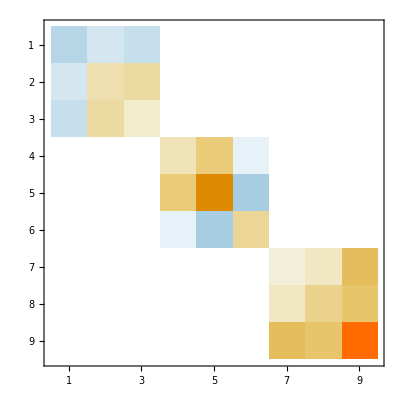

```mathematica
Normal[
SparseArray[
Band[{1, 1}]->
ArrayReshape[
goup,
{3,3, 3}
]
]
]//MatrixPlot
```

```mathematica
Export[
"~/Desktop/agh.dat",
Normal[
SparseArray[
Band[{1, 1}]->
ArrayReshape[
goup,
{3,3, 3}
]
]
],
"Table"
]
```

~/Desktop/agh.dat

```mathematica
ArrayReshape[
goup,
{3,3, 3}
]
```

{{{-37.0394,-32.3039,-33.0822},{-32.3039,3.57148,9.77125},{-33.0822,9.77125,3.08397}},{{3.53205,66.3537,-8.46713},{66.3537,804.479,-51.44},{-8.46713,-51.44,10.6009}},{{2.67362,3.14498,111.807},{3.14498,10.6015,97.0564},{111.807,97.0564,1519.01}}}

```mathematica
Join[
{
Flatten[goup],
bloop,
Flatten[goup]-bloop
}//Transpose,
goodShit[[All, 2;;]],
2
]//Grid
```

-37.0394 | -37.037130862977186 | -0.00223914 | 1 | 1 | 1
-32.3039 | -44.9157018563210997 | 12.6118 | 2 | 1 | 1
-33.0822 | -13.1585571611089804 | -19.9236 | 3 | 1 | 1
-32.3039 | -44.9157018730646769 | 12.6118 | 1 | 2 | 1
3.57148 | 159.875111566850421 | -156.304 | 2 | 2 | 1
9.77125 | 52.6874274762919441 | -42.9162 | 3 | 2 | 1
-33.0822 | -13.1585571425285135 | -19.9236 | 1 | 3 | 1
9.77125 | 52.6874274769239648 | -42.9162 | 2 | 3 | 1
3.08397 | 705.988614799319635 | -702.905 | 3 | 3 | 1
3.53205 | 159.852866260348662 | -156.321 | 1 | 1 | 2
66.3537 | 70.5363941993188917 | -4.18265 | 2 | 1 | 2
-8.46713 | -17.3517153553032699 | 8.88458 | 3 | 1 | 2
66.3537 | 70.5363941608842282 | -4.18265 | 1 | 2 | 2
804.479 | 804.479853052713679 | -0.00113982 | 2 | 2 | 2
-51.44 | -51.5094702834340836 | 0.0694239 | 3 | 2 | 2
-8.46713 | -17.3517153155611474 | 8.88458 | 1 | 3 | 2
-51.44 | -51.5094702876772246 | 0.0694239 | 2 | 3 | 2
10.6009 | 10.8046715301098484 | -0.203805 | 3 | 3 | 2
2.67362 | 705.73781485545544 | -703.064 | 1 | 1 | 3
3.14498 | -3.81244180059036131 | 6.95742 | 2 | 1 | 3
111.807 | 121.914562838758087 | -10.1077 | 3 | 1 | 3
3.14498 | -3.81244181149977734 | 6.95742 | 1 | 2 | 3
10.6015 | 10.8051237130365365 | -0.203586 | 2 | 2 | 3
97.0564 | 97.072176652327002 | -0.0157429 | 3 | 2 | 3
111.807 | 121.914562801415769 | -10.1077 | 1 | 3 | 3
97.0564 | 97.0721766610977426 | -0.0157429 | 2 | 3 | 3
1519.01 | 1519.00669792001486 | -0.00067515 | 3 | 3 | 3

```mathematica
bloop2=Import["~/Desktop/bleh.dat"]//Flatten;
```

```mathematica
{
Flatten[goup],
bloop2,
Flatten[goup]-bloop2
}//Transpose//Gridf
```

-37.0394 | 38.4794208791187771 | -75.5188
-32.3039 | -39.2914529344690777 | 6.98754
-33.0822 | -15.3194626832733665 | -17.7627
-32.3039 | -39.2914529344321508 | 6.98754
3.57148 | 185.855188612835264 | -182.284
9.77125 | 64.4422443026192866 | -54.671
-33.0822 | -15.3194626831602179 | -17.7627
9.77125 | 64.4422443026192582 | -54.671
3.08397 | 830.728728951937114 | -827.645
3.53205 | 185.83294323433509 | -182.301
66.3537 | 62.7600939535868676 | 3.59365
-8.46713 | -8.53890212669570481 | 0.0717709
66.3537 | 62.7600939535869387 | 3.59365
804.479 | 804.660199246466732 | -0.181486
-51.44 | -51.5671470781781096 | 0.127101
-8.46713 | -8.53890212669586823 | 0.0717709
-51.44 | -51.5671470781781522 | 0.127101
10.6009 | 10.95913701504392 | -0.35827
2.67362 | 830.477928794180343 | -827.804
3.14498 | -5.13156057243419728 | 8.27654
111.807 | 111.963159272142292 | -0.156338
3.14498 | -5.13156057243568675 | 8.27654
10.6015 | 10.9595891896989599 | -0.358052
97.0564 | 96.7582360251977036 | 0.298198
111.807 | 111.96315927214215 | -0.156338
97.0564 | 96.7582360251976468 | 0.298198
1519.01 | 1519.53032516467306 | -0.524302